```mathematica
ShowGraph[Graph[{1 2,2 3}]]
```

ShowGraph[Graph[{2,6}]]



```mathematica
Graph[{1<->2,2<->3}]
```



```mathematica
Graph[{1<->2,2<->3,1<->3}]
```

```mathematica
Graph[{{1,27,110},{1,12,1500},{1,16,340},{1,7,340},{1,22,0},{2,10,210},{2,9,90},{2,14,240},{2,30,240},{3,10,430},{3,15,195},{3,19,195},{3,24,1255},{4,21,650},{4,18,870},{4,29,740},{4,6,230},{4,5,460},{5,21,560},{5,30,415},{5,14,415},{5,17,235},{5,4,460},{6,18,1115},{6,13,790},{6,24,965},{6,4,230},{7,16,0},{7,11,680},{7,18,650},{7,22,340},{7,1,340},{8,26,0},{8,20,90},{8,28,195},{8,29,560},{8,24,930},{9,2,90},{9,23,225},{9,28,115},{10,3,430},{10,11,2070},{10,25,430},{10,2,210},{10,28,225},{11,16,680},{11,10,2070},{11,12,1390},{12,11,1390},{12,22,1500},{12,1,1500},{12,17,465},{12,25,300},{13,23,790},{13,6,790},{13,24,210},{14,30,0},{14,25,80},{14,2,240},{14,23,250},{14,5,415},{15,3,195},{15,19,0},{15,20,80},{15,28,315},{16,11,680},{16,7,0},{16,22,340},{16,1,340},{16,18,650},{17,6,680},{17,5,235},{17,23,310},{17,12,465},{18,16,650},{18,7,650},{18,27,300},{18,21,580},{18,4,870},{18,6,1115},{19,15,0},{19,20,80},{19,3,195},{19,28,315},{20,15,80},{20,19,80},{20,8,90},{20,26,90},{21,5,560},{21,4,650},{21,18,580},{21,27,830},{22,1,0},{22,27,110},{22,16,340},{22,7,340},{22,12,1500},{23,17,310},{23,29,375},{23,13,790},{23,28,260},{23,9,225},{23,14,250},{23,30,250},{24,13,210},{24,6,965},{24,3,1255},{24,26,930},{24,8,930},{24,29,600},{25,12,300},{25,30,80},{25,14,80},{25,10,430},{26,8,0},{26,28,195},{26,29,560},{26,24,930},{26,20,90},{27,22,110},{27,1,110},{27,18,300},{27,21,830},{28,9,115},{28,23,260},{28,8,195},{28,26,195},{28,19,315},{28,15,315},{28,10,225},{29,4,740},{29,24,600},{29,8,560},{29,26,560},{29,23,375},{30,14,0},{30,25,80},{30,5,415},{30,2,240},{30,23,250}}]
```

Graph[{{1,27,110},{1,12,1500},{1,16,340},{1,7,340},{1,22,0},{2,10,210},{2,9,90},{2,14,240},{2,30,240},{3,10,430},{3,15,195},{3,19,195},{3,24,1255},{4,21,650},{4,18,870},{4,29,740},{4,6,230},{4,5,460},{5,21,560},{5,30,415},{5,14,415},{5,17,235},{5,4,460},{6,18,1115},{6,13,790},{6,24,965},{6,4,230},{7,16,0},{7,11,680},{7,18,650},{7,22,340},{7,1,340},{8,26,0},{8,20,90},{8,28,195},{8,29,560},{8,24,930},{9,2,90},{9,23,225},{9,28,115},{10,3,430},{10,11,2070},{10,25,430},{10,2,210},{10,28,225},{11,16,680},{11,10,2070},{11,12,1390},{12,11,1390},{12,22,1500},{12,1,1500},{12,17,465},{12,25,300},{13,23,790},{13,6,790},{13,24,210},{14,30,0},{14,25,80},{14,2,240},{14,23,250},{14,5,415},{15,3,195},{15,19,0},{15,20,80},{15,28,315},{16,11,680},{16,7,0},{16,22,340},{16,1,340},{16,18,650},{17,6,680},{17,5,235},{17,23,310},{17,12,465},{18,16,650},{18,7,650},{18,27,300},{18,21,580},{18,4,870},{18,6,1115},{19,15,0},{19,20,80},{19,3,195},{19,28,315},{20,15,80},{20,19,80},{20,8,90},{20,26,90},{21,5,560},{21,4,650},{21,18,580},{21,27,830},{22,1,0},{22,27,110},{22,16,340},{22,7,340},{22,12,1500},{23,17,310},{23,29,375},{23,13,790},{23,28,260},{23,9,225},{23,14,250},{23,30,250},{24,13,210},{24,6,965},{24,3,1255},{24,26,930},{24,8,930},{24,29,600},{25,12,300},{25,30,80},{25,14,80},{25,10,430},{26,8,0},{26,28,195},{26,29,560},{26,24,930},{26,20,90},{27,22,110},{27,1,110},{27,18,300},{27,21,830},{28,9,115},{28,23,260},{28,8,195},{28,26,195},{28,19,315},{28,15,315},{28,10,225},{29,4,740},{29,24,600},{29,8,560},{29,26,560},{29,23,375},{30,14,0},{30,25,80},{30,5,415},{30,2,240},{30,23,250}}]

```mathematica
myGraph = WeightedAdjacencyGraph[{{1<->27,110},{27<->1,110}}]
```

-Graphics-

```mathematica
myAdjMatrix = {{-1,-1,-1,-1,-1,-1,340,-1,-1,-1,-1,1500,-1,-1,-1,340,-1,-1,-1,-1,-1,0,-1,-1,-1,-1,110,-1,-1,-1},
{-1,-1,-1,-1,-1,-1,-1,-1,90,210,-1,-1,-1,240,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,240},
{-1,-1,-1,-1,-1,-1,-1,-1,-1,430,-1,-1,-1,-1,195,-1,-1,-1,195,-1,-1,-1,-1,1255,-1,-1,-1,-1,-1,-1},
{-1,-1,-1,-1,460,230,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,870,-1,-1,650,-1,-1,-1,-1,-1,-1,-1,740,-1},
{-1,-1,-1,460,-1,-1,-1,-1,-1,-1,-1,-1,-1,415,-1,-1,235,-1,-1,-1,560,-1,-1,-1,-1,-1,-1,-1,-1,415},
{-1,-1,-1,230,-1,-1,-1,-1,-1,-1,-1,-1,790,-1,-1,-1,-1,1115,-1,-1,-1,-1,-1,965,-1,-1,-1,-1,-1,-1},
{340,-1,-1,-1,-1,-1,-1,-1,-1,-1,680,-1,-1,-1,-1,0,-1,650,-1,-1,-1,340,-1,-1,-1,-1,-1,-1,-1,-1},
{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,90,-1,-1,-1,930,-1,0,-1,195,560,-1},
{-1,90,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,225,-1,-1,-1,-1,115,-1,-1},
{-1,210,430,-1,-1,-1,-1,-1,-1,-1,2070,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,430,-1,-1,225,-1,-1},
{-1,-1,-1,-1,-1,-1,-1,-1,-1,2070,-1,1390,-1,-1,-1,680,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},
{1500,-1,-1,-1,-1,-1,-1,-1,-1,-1,1390,-1,-1,-1,-1,-1,465,-1,-1,-1,-1,1500,-1,-1,300,-1,-1,-1,-1,-1},
{-1,-1,-1,-1,-1,790,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,790,210,-1,-1,-1,-1,-1,-1},
{-1,240,-1,-1,415,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,250,-1,80,-1,-1,-1,-1,0},
{-1,-1,195,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,80,-1,-1,-1,-1,-1,-1,-1,315,-1,-1},
{340,-1,-1,-1,-1,-1,0,-1,-1,-1,680,-1,-1,-1,-1,-1,-1,650,-1,-1,-1,340,-1,-1,-1,-1,-1,-1,-1,-1},
{-1,-1,-1,-1,235,680,-1,-1,-1,-1,-1,465,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,310,-1,-1,-1,-1,-1,-1,-1},
{-1,-1,-1,870,-1,1115,650,-1,-1,-1,-1,-1,-1,-1,-1,650,-1,-1,-1,-1,580,-1,-1,-1,-1,-1,300,-1,-1,-1},
{-1,-1,195,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,-1,-1,-1,-1,80,-1,-1,-1,-1,-1,-1,-1,315,-1,-1},
{-1,-1,-1,-1,-1,-1,-1,90,-1,-1,-1,-1,-1,-1,80,-1,-1,-1,80,-1,-1,-1,-1,-1,-1,90,-1,-1,-1,-1},
{-1,-1,-1,650,560,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,580,-1,-1,-1,-1,-1,-1,-1,-1,830,-1,-1,-1},
{0,-1,-1,-1,-1,-1,340,-1,-1,-1,-1,1500,-1,-1,-1,340,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,110,-1,-1,-1},
{-1,-1,-1,-1,-1,-1,-1,-1,225,-1,-1,-1,790,250,-1,-1,310,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,260,375,250},
{-1,-1,1255,-1,-1,965,-1,930,-1,-1,-1,-1,210,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,930,-1,-1,600,-1},
{-1,-1,-1,-1,-1,-1,-1,-1,-1,430,-1,300,-1,80,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,80},
{-1,-1,-1,-1,-1,-1,-1,0,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,90,-1,-1,-1,930,-1,-1,-1,195,560,-1},
{110,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,300,-1,-1,830,110,-1,-1,-1,-1,-1,-1,-1,-1},
{-1,-1,-1,-1,-1,-1,-1,195,115,225,-1,-1,-1,-1,315,-1,-1,-1,315,-1,-1,-1,260,-1,-1,195,-1,-1,-1,-1},
{-1,-1,-1,740,-1,-1,-1,560,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,375,600,-1,560,-1,-1,-1,-1},
{-1,240,-1,-1,415,-1,-1,-1,-1,-1,-1,-1,-1,0,-1,-1,-1,-1,-1,-1,-1,-1,250,-1,80,-1,-1,-1,-1,-1}} /. -1 -> Infinity
```

{{∞,∞,∞,∞,∞,∞,340,∞,∞,∞,∞,1500,∞,∞,∞,340,∞,∞,∞,∞,∞,0,∞,∞,∞,∞,110,∞,∞,∞},{∞,∞,∞,∞,∞,∞,∞,∞,90,210,∞,∞,∞,240,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,240},{∞,∞,∞,∞,∞,∞,∞,∞,∞,430,∞,∞,∞,∞,195,∞,∞,∞,195,∞,∞,∞,∞,1255,∞,∞,∞,∞,∞,∞},{∞,∞,∞,∞,460,230,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,870,∞,∞,650,∞,∞,∞,∞,∞,∞,∞,740,∞},{∞,∞,∞,460,∞,∞,∞,∞,∞,∞,∞,∞,∞,415,∞,∞,235,∞,∞,∞,560,∞,∞,∞,∞,∞,∞,∞,∞,415},{∞,∞,∞,230,∞,∞,∞,∞,∞,∞,∞,∞,790,∞,∞,∞,∞,1115,∞,∞,∞,∞,∞,965,∞,∞,∞,∞,∞,∞},{340,∞,∞,∞,∞,∞,∞,∞,∞,∞,680,∞,∞,∞,∞,0,∞,650,∞,∞,∞,340,∞,∞,∞,∞,∞,∞,∞,∞},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,90,∞,∞,∞,930,∞,0,∞,195,560,∞},{∞,90,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,225,∞,∞,∞,∞,115,∞,∞},{∞,210,430,∞,∞,∞,∞,∞,∞,∞,2070,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,430,∞,∞,225,∞,∞},{∞,∞,∞,∞,∞,∞,∞,∞,∞,2070,∞,1390,∞,∞,∞,680,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞},{1500,∞,∞,∞,∞,∞,∞,∞,∞,∞,1390,∞,∞,∞,∞,∞,465,∞,∞,∞,∞,1500,∞,∞,300,∞,∞,∞,∞,∞},{∞,∞,∞,∞,∞,790,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,790,210,∞,∞,∞,∞,∞,∞},{∞,240,∞,∞,415,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,250,∞,80,∞,∞,∞,∞,0},{∞,∞,195,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,0,80,∞,∞,∞,∞,∞,∞,∞,315,∞,∞},{340,∞,∞,∞,∞,∞,0,∞,∞,∞,680,∞,∞,∞,∞,∞,∞,650,∞,∞,∞,340,∞,∞,∞,∞,∞,∞,∞,∞},{∞,∞,∞,∞,235,680,∞,∞,∞,∞,∞,465,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,310,∞,∞,∞,∞,∞,∞,∞},{∞,∞,∞,870,∞,1115,650,∞,∞,∞,∞,∞,∞,∞,∞,650,∞,∞,∞,∞,580,∞,∞,∞,∞,∞,300,∞,∞,∞},{∞,∞,195,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,0,∞,∞,∞,∞,80,∞,∞,∞,∞,∞,∞,∞,315,∞,∞},{∞,∞,∞,∞,∞,∞,∞,90,∞,∞,∞,∞,∞,∞,80,∞,∞,∞,80,∞,∞,∞,∞,∞,∞,90,∞,∞,∞,∞},{∞,∞,∞,650,560,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,580,∞,∞,∞,∞,∞,∞,∞,∞,830,∞,∞,∞},{0,∞,∞,∞,∞,∞,340,∞,∞,∞,∞,1500,∞,∞,∞,340,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,110,∞,∞,∞},{∞,∞,∞,∞,∞,∞,∞,∞,225,∞,∞,∞,790,250,∞,∞,310,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,260,375,250},{∞,∞,1255,∞,∞,965,∞,930,∞,∞,∞,∞,210,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,930,∞,∞,600,∞},{∞,∞,∞,∞,∞,∞,∞,∞,∞,430,∞,300,∞,80,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,80},{∞,∞,∞,∞,∞,∞,∞,0,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,90,∞,∞,∞,930,∞,∞,∞,195,560,∞},{110,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,300,∞,∞,830,110,∞,∞,∞,∞,∞,∞,∞,∞},{∞,∞,∞,∞,∞,∞,∞,195,115,225,∞,∞,∞,∞,315,∞,∞,∞,315,∞,∞,∞,260,∞,∞,195,∞,∞,∞,∞},{∞,∞,∞,740,∞,∞,∞,560,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,375,600,∞,560,∞,∞,∞,∞},{∞,240,∞,∞,415,∞,∞,∞,∞,∞,∞,∞,∞,0,∞,∞,∞,∞,∞,∞,∞,∞,250,∞,80,∞,∞,∞,∞,∞}}

```mathematica
f[pts_List, e_] :=
	Block[{s= 0.015, weight = PropertyValue[{g, e}, EdgeWeight]},
	{Arrowheads[{{s, 0.01}, {s, 0.05}}],
	AbsoluteThickness[weight * .01],
	Arrow[pts]}]
```

```mathematica
g = WeightedAdjacencyGraph[myAdjMatrix,
	VertexLabels->"Name",
	EdgeLabels-> "EdgeWeight",
	EdgeShapeFunction->f,
	VertexLabelStyle -> UndirectedEdge[Red,18]];
```

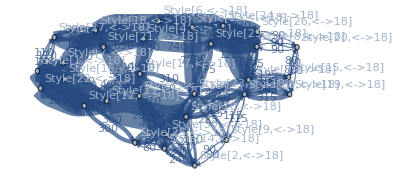

```mathematica
Show[g]
```

```mathematica
Show[%64,ImageSize->Full]
```

-Graphics-

```mathematica
FindShortestPath[g,21, All]
```

ShortestPathFunction[{21,All},«»]

```mathematica
%72[5]
```

{21,5}

```mathematica
%72[4]
```

{21,4}

```mathematica
%72[3]
```

{21,5,14,2,10,3}

```mathematica
%72[2]
```

{21,5,14,2}

```mathematica
%72[1]
```

{21,27,1}

```mathematica
MinimumSpanningTree[g]
```

MinimumSpanningTree[-Graphics-]

```mathematica
ShowGraph[%]
```

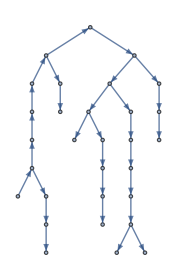

```mathematica
FindSpanningTree[g]
```

```mathematica
m ={{3 3 2},{1 3 4}}
```

{{18},{12}}

```mathematica
Graph[{1->2,2->3,3->1},EdgeWeight->RandomReal[{1,5},3],EdgeStyle->Arrowheads[.06]];
WeightedAdjacencyMatrix[%]//MatrixForm
```

(0 | 4.26192 | 0
0 | 0 | 1.07869
4.05182 | 0 | 0)

```mathematica
m = {{-1,-1,-1,-1,-1,-1,340,-1,-1,-1,-1,1500,-1,-1,-1,340,-1,-1,-1,-1,-1,0,-1,-1,-1,-1,110,-1,-1,-1},{-1,-1,-1,-1,-1,-1,-1,-1,90,210,-1,-1,-1,240,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,240},{-1,-1,-1,-1,-1,-1,-1,-1,-1,430,-1,-1,-1,-1,195,-1,-1,-1,195,-1,-1,-1,-1,1255,-1,-1,-1,-1,-1,-1},{-1,-1,-1,-1,460,230,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,870,-1,-1,650,-1,-1,-1,-1,-1,-1,-1,740,-1},{-1,-1,-1,460,-1,-1,-1,-1,-1,-1,-1,-1,-1,415,-1,-1,235,-1,-1,-1,560,-1,-1,-1,-1,-1,-1,-1,-1,415},{-1,-1,-1,230,-1,-1,-1,-1,-1,-1,-1,-1,790,-1,-1,-1,-1,1115,-1,-1,-1,-1,-1,965,-1,-1,-1,-1,-1,-1},{340,-1,-1,-1,-1,-1,-1,-1,-1,-1,680,-1,-1,-1,-1,0,-1,650,-1,-1,-1,340,-1,-1,-1,-1,-1,-1,-1,-1},{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,90,-1,-1,-1,930,-1,0,-1,195,560,-1},{-1,90,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,225,-1,-1,-1,-1,115,-1,-1},{-1,210,430,-1,-1,-1,-1,-1,-1,-1,2070,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,430,-1,-1,225,-1,-1},{-1,-1,-1,-1,-1,-1,-1,-1,-1,2070,-1,1390,-1,-1,-1,680,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{1500,-1,-1,-1,-1,-1,-1,-1,-1,-1,1390,-1,-1,-1,-1,-1,465,-1,-1,-1,-1,1500,-1,-1,300,-1,-1,-1,-1,-1},{-1,-1,-1,-1,-1,790,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,790,210,-1,-1,-1,-1,-1,-1},{-1,240,-1,-1,415,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,250,-1,80,-1,-1,-1,-1,0},{-1,-1,195,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,80,-1,-1,-1,-1,-1,-1,-1,315,-1,-1},{340,-1,-1,-1,-1,-1,0,-1,-1,-1,680,-1,-1,-1,-1,-1,-1,650,-1,-1,-1,340,-1,-1,-1,-1,-1,-1,-1,-1},{-1,-1,-1,-1,235,680,-1,-1,-1,-1,-1,465,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,310,-1,-1,-1,-1,-1,-1,-1},{-1,-1,-1,870,-1,1115,650,-1,-1,-1,-1,-1,-1,-1,-1,650,-1,-1,-1,-1,580,-1,-1,-1,-1,-1,300,-1,-1,-1},{-1,-1,195,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,-1,-1,-1,-1,80,-1,-1,-1,-1,-1,-1,-1,315,-1,-1},{-1,-1,-1,-1,-1,-1,-1,90,-1,-1,-1,-1,-1,-1,80,-1,-1,-1,80,-1,-1,-1,-1,-1,-1,90,-1,-1,-1,-1},{-1,-1,-1,650,560,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,580,-1,-1,-1,-1,-1,-1,-1,-1,830,-1,-1,-1},{0,-1,-1,-1,-1,-1,340,-1,-1,-1,-1,1500,-1,-1,-1,340,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,110,-1,-1,-1},{-1,-1,-1,-1,-1,-1,-1,-1,225,-1,-1,-1,790,250,-1,-1,310,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,260,375,250},{-1,-1,1255,-1,-1,965,-1,930,-1,-1,-1,-1,210,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,930,-1,-1,600,-1},{-1,-1,-1,-1,-1,-1,-1,-1,-1,430,-1,300,-1,80,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,80},{-1,-1,-1,-1,-1,-1,-1,0,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,90,-1,-1,-1,930,-1,-1,-1,195,560,-1},{110,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,300,-1,-1,830,110,-1,-1,-1,-1,-1,-1,-1,-1},{-1,-1,-1,-1,-1,-1,-1,195,115,225,-1,-1,-1,-1,315,-1,-1,-1,315,-1,-1,-1,260,-1,-1,195,-1,-1,-1,-1},{-1,-1,-1,740,-1,-1,-1,560,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,375,600,-1,560,-1,-1,-1,-1},{-1,240,-1,-1,415,-1,-1,-1,-1,-1,-1,-1,-1,0,-1,-1,-1,-1,-1,-1,-1,-1,250,-1,80,-1,-1,-1,-1,-1}} /. -1-> Infinity
```

{{∞,∞,∞,∞,∞,∞,340,∞,∞,∞,∞,1500,∞,∞,∞,340,∞,∞,∞,∞,∞,0,∞,∞,∞,∞,110,∞,∞,∞},{∞,∞,∞,∞,∞,∞,∞,∞,90,210,∞,∞,∞,240,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,240},{∞,∞,∞,∞,∞,∞,∞,∞,∞,430,∞,∞,∞,∞,195,∞,∞,∞,195,∞,∞,∞,∞,1255,∞,∞,∞,∞,∞,∞},{∞,∞,∞,∞,460,230,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,870,∞,∞,650,∞,∞,∞,∞,∞,∞,∞,740,∞},{∞,∞,∞,460,∞,∞,∞,∞,∞,∞,∞,∞,∞,415,∞,∞,235,∞,∞,∞,560,∞,∞,∞,∞,∞,∞,∞,∞,415},{∞,∞,∞,230,∞,∞,∞,∞,∞,∞,∞,∞,790,∞,∞,∞,∞,1115,∞,∞,∞,∞,∞,965,∞,∞,∞,∞,∞,∞},{340,∞,∞,∞,∞,∞,∞,∞,∞,∞,680,∞,∞,∞,∞,0,∞,650,∞,∞,∞,340,∞,∞,∞,∞,∞,∞,∞,∞},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,90,∞,∞,∞,930,∞,0,∞,195,560,∞},{∞,90,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,225,∞,∞,∞,∞,115,∞,∞},{∞,210,430,∞,∞,∞,∞,∞,∞,∞,2070,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,430,∞,∞,225,∞,∞},{∞,∞,∞,∞,∞,∞,∞,∞,∞,2070,∞,1390,∞,∞,∞,680,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞},{1500,∞,∞,∞,∞,∞,∞,∞,∞,∞,1390,∞,∞,∞,∞,∞,465,∞,∞,∞,∞,1500,∞,∞,300,∞,∞,∞,∞,∞},{∞,∞,∞,∞,∞,790,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,790,210,∞,∞,∞,∞,∞,∞},{∞,240,∞,∞,415,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,250,∞,80,∞,∞,∞,∞,0},{∞,∞,195,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,0,80,∞,∞,∞,∞,∞,∞,∞,315,∞,∞},{340,∞,∞,∞,∞,∞,0,∞,∞,∞,680,∞,∞,∞,∞,∞,∞,650,∞,∞,∞,340,∞,∞,∞,∞,∞,∞,∞,∞},{∞,∞,∞,∞,235,680,∞,∞,∞,∞,∞,465,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,310,∞,∞,∞,∞,∞,∞,∞},{∞,∞,∞,870,∞,1115,650,∞,∞,∞,∞,∞,∞,∞,∞,650,∞,∞,∞,∞,580,∞,∞,∞,∞,∞,300,∞,∞,∞},{∞,∞,195,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,0,∞,∞,∞,∞,80,∞,∞,∞,∞,∞,∞,∞,315,∞,∞},{∞,∞,∞,∞,∞,∞,∞,90,∞,∞,∞,∞,∞,∞,80,∞,∞,∞,80,∞,∞,∞,∞,∞,∞,90,∞,∞,∞,∞},{∞,∞,∞,650,560,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,580,∞,∞,∞,∞,∞,∞,∞,∞,830,∞,∞,∞},{0,∞,∞,∞,∞,∞,340,∞,∞,∞,∞,1500,∞,∞,∞,340,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,110,∞,∞,∞},{∞,∞,∞,∞,∞,∞,∞,∞,225,∞,∞,∞,790,250,∞,∞,310,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,260,375,250},{∞,∞,1255,∞,∞,965,∞,930,∞,∞,∞,∞,210,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,930,∞,∞,600,∞},{∞,∞,∞,∞,∞,∞,∞,∞,∞,430,∞,300,∞,80,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,80},{∞,∞,∞,∞,∞,∞,∞,0,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,90,∞,∞,∞,930,∞,∞,∞,195,560,∞},{110,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,300,∞,∞,830,110,∞,∞,∞,∞,∞,∞,∞,∞},{∞,∞,∞,∞,∞,∞,∞,195,115,225,∞,∞,∞,∞,315,∞,∞,∞,315,∞,∞,∞,260,∞,∞,195,∞,∞,∞,∞},{∞,∞,∞,740,∞,∞,∞,560,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,375,600,∞,560,∞,∞,∞,∞},{∞,240,∞,∞,415,∞,∞,∞,∞,∞,∞,∞,∞,0,∞,∞,∞,∞,∞,∞,∞,∞,250,∞,80,∞,∞,∞,∞,∞}}

```mathematica
MatrixForm[m]
```

(∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 340 | ∞ | ∞ | ∞ | ∞ | 1500 | ∞ | ∞ | ∞ | 340 | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | ∞ | ∞ | ∞ | ∞ | 110 | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 90 | 210 | ∞ | ∞ | ∞ | 240 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 240
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 430 | ∞ | ∞ | ∞ | ∞ | 195 | ∞ | ∞ | ∞ | 195 | ∞ | ∞ | ∞ | ∞ | 1255 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | 460 | 230 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 870 | ∞ | ∞ | 650 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 740 | ∞
∞ | ∞ | ∞ | 460 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 415 | ∞ | ∞ | 235 | ∞ | ∞ | ∞ | 560 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 415
∞ | ∞ | ∞ | 230 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 790 | ∞ | ∞ | ∞ | ∞ | 1115 | ∞ | ∞ | ∞ | ∞ | ∞ | 965 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
340 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 680 | ∞ | ∞ | ∞ | ∞ | 0 | ∞ | 650 | ∞ | ∞ | ∞ | 340 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 90 | ∞ | ∞ | ∞ | 930 | ∞ | 0 | ∞ | 195 | 560 | ∞
∞ | 90 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 225 | ∞ | ∞ | ∞ | ∞ | 115 | ∞ | ∞
∞ | 210 | 430 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2070 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 430 | ∞ | ∞ | 225 | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2070 | ∞ | 1390 | ∞ | ∞ | ∞ | 680 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
1500 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1390 | ∞ | ∞ | ∞ | ∞ | ∞ | 465 | ∞ | ∞ | ∞ | ∞ | 1500 | ∞ | ∞ | 300 | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | 790 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 790 | 210 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | 240 | ∞ | ∞ | 415 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 250 | ∞ | 80 | ∞ | ∞ | ∞ | ∞ | 0
∞ | ∞ | 195 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 80 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 315 | ∞ | ∞
340 | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | ∞ | ∞ | ∞ | 680 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 650 | ∞ | ∞ | ∞ | 340 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | 235 | 680 | ∞ | ∞ | ∞ | ∞ | ∞ | 465 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 310 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | 870 | ∞ | 1115 | 650 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 650 | ∞ | ∞ | ∞ | ∞ | 580 | ∞ | ∞ | ∞ | ∞ | ∞ | 300 | ∞ | ∞ | ∞
∞ | ∞ | 195 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | ∞ | ∞ | ∞ | ∞ | 80 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 315 | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 90 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 80 | ∞ | ∞ | ∞ | 80 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 90 | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | 650 | 560 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 580 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 830 | ∞ | ∞ | ∞
0 | ∞ | ∞ | ∞ | ∞ | ∞ | 340 | ∞ | ∞ | ∞ | ∞ | 1500 | ∞ | ∞ | ∞ | 340 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 110 | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 225 | ∞ | ∞ | ∞ | 790 | 250 | ∞ | ∞ | 310 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 260 | 375 | 250
∞ | ∞ | 1255 | ∞ | ∞ | 965 | ∞ | 930 | ∞ | ∞ | ∞ | ∞ | 210 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 930 | ∞ | ∞ | 600 | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 430 | ∞ | 300 | ∞ | 80 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 80
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 90 | ∞ | ∞ | ∞ | 930 | ∞ | ∞ | ∞ | 195 | 560 | ∞
110 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 300 | ∞ | ∞ | 830 | 110 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 195 | 115 | 225 | ∞ | ∞ | ∞ | ∞ | 315 | ∞ | ∞ | ∞ | 315 | ∞ | ∞ | ∞ | 260 | ∞ | ∞ | 195 | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | 740 | ∞ | ∞ | ∞ | 560 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 375 | 600 | ∞ | 560 | ∞ | ∞ | ∞ | ∞
∞ | 240 | ∞ | ∞ | 415 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 250 | ∞ | 80 | ∞ | ∞ | ∞ | ∞ | ∞)

```mathematica
MatrixForm[m]
```

(∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 340 | ∞ | ∞ | ∞ | ∞ | 1500 | ∞ | ∞ | ∞ | 340 | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | ∞ | ∞ | ∞ | ∞ | 110 | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 90 | 210 | ∞ | ∞ | ∞ | 240 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 240
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 430 | ∞ | ∞ | ∞ | ∞ | 195 | ∞ | ∞ | ∞ | 195 | ∞ | ∞ | ∞ | ∞ | 1255 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | 460 | 230 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 870 | ∞ | ∞ | 650 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 740 | ∞
∞ | ∞ | ∞ | 460 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 415 | ∞ | ∞ | 235 | ∞ | ∞ | ∞ | 560 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 415
∞ | ∞ | ∞ | 230 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 790 | ∞ | ∞ | ∞ | ∞ | 1115 | ∞ | ∞ | ∞ | ∞ | ∞ | 965 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
340 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 680 | ∞ | ∞ | ∞ | ∞ | 0 | ∞ | 650 | ∞ | ∞ | ∞ | 340 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 90 | ∞ | ∞ | ∞ | 930 | ∞ | 0 | ∞ | 195 | 560 | ∞
∞ | 90 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 225 | ∞ | ∞ | ∞ | ∞ | 115 | ∞ | ∞
∞ | 210 | 430 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2070 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 430 | ∞ | ∞ | 225 | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2070 | ∞ | 1390 | ∞ | ∞ | ∞ | 680 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
1500 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1390 | ∞ | ∞ | ∞ | ∞ | ∞ | 465 | ∞ | ∞ | ∞ | ∞ | 1500 | ∞ | ∞ | 300 | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | 790 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 790 | 210 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | 240 | ∞ | ∞ | 415 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 250 | ∞ | 80 | ∞ | ∞ | ∞ | ∞ | 0
∞ | ∞ | 195 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 80 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 315 | ∞ | ∞
340 | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | ∞ | ∞ | ∞ | 680 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 650 | ∞ | ∞ | ∞ | 340 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | 235 | 680 | ∞ | ∞ | ∞ | ∞ | ∞ | 465 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 310 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | 870 | ∞ | 1115 | 650 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 650 | ∞ | ∞ | ∞ | ∞ | 580 | ∞ | ∞ | ∞ | ∞ | ∞ | 300 | ∞ | ∞ | ∞
∞ | ∞ | 195 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | ∞ | ∞ | ∞ | ∞ | 80 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 315 | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 90 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 80 | ∞ | ∞ | ∞ | 80 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 90 | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | 650 | 560 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 580 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 830 | ∞ | ∞ | ∞
0 | ∞ | ∞ | ∞ | ∞ | ∞ | 340 | ∞ | ∞ | ∞ | ∞ | 1500 | ∞ | ∞ | ∞ | 340 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 110 | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 225 | ∞ | ∞ | ∞ | 790 | 250 | ∞ | ∞ | 310 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 260 | 375 | 250
∞ | ∞ | 1255 | ∞ | ∞ | 965 | ∞ | 930 | ∞ | ∞ | ∞ | ∞ | 210 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 930 | ∞ | ∞ | 600 | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 430 | ∞ | 300 | ∞ | 80 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 80
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 90 | ∞ | ∞ | ∞ | 930 | ∞ | ∞ | ∞ | 195 | 560 | ∞
110 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 300 | ∞ | ∞ | 830 | 110 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 195 | 115 | 225 | ∞ | ∞ | ∞ | ∞ | 315 | ∞ | ∞ | ∞ | 315 | ∞ | ∞ | ∞ | 260 | ∞ | ∞ | 195 | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | 740 | ∞ | ∞ | ∞ | 560 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 375 | 600 | ∞ | 560 | ∞ | ∞ | ∞ | ∞
∞ | 240 | ∞ | ∞ | 415 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 250 | ∞ | 80 | ∞ | ∞ | ∞ | ∞ | ∞)

```mathematica
WeightedAdjacencyMatrix[g]
```

SparseArray[<140>, {30, 30}]

```mathematica
MatrixForm[m]
```

```mathematica
ge = Graph[m]
```

Graph[{{∞,∞,∞,∞,∞,∞,340,∞,∞,∞,∞,1500,∞,∞,∞,340,∞,∞,∞,∞,∞,0,∞,∞,∞,∞,110,∞,∞,∞},{∞,∞,∞,∞,∞,∞,∞,∞,90,210,∞,∞,∞,240,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,240},{∞,∞,∞,∞,∞,∞,∞,∞,∞,430,∞,∞,∞,∞,195,∞,∞,∞,195,∞,∞,∞,∞,1255,∞,∞,∞,∞,∞,∞},{∞,∞,∞,∞,460,230,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,870,∞,∞,650,∞,∞,∞,∞,∞,∞,∞,740,∞},{∞,∞,∞,460,∞,∞,∞,∞,∞,∞,∞,∞,∞,415,∞,∞,235,∞,∞,∞,560,∞,∞,∞,∞,∞,∞,∞,∞,415},{∞,∞,∞,230,∞,∞,∞,∞,∞,∞,∞,∞,790,∞,∞,∞,∞,1115,∞,∞,∞,∞,∞,965,∞,∞,∞,∞,∞,∞},{340,∞,∞,∞,∞,∞,∞,∞,∞,∞,680,∞,∞,∞,∞,0,∞,650,∞,∞,∞,340,∞,∞,∞,∞,∞,∞,∞,∞},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,90,∞,∞,∞,930,∞,0,∞,195,560,∞},{∞,90,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,225,∞,∞,∞,∞,115,∞,∞},{∞,210,430,∞,∞,∞,∞,∞,∞,∞,2070,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,430,∞,∞,225,∞,∞},{∞,∞,∞,∞,∞,∞,∞,∞,∞,2070,∞,1390,∞,∞,∞,680,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞},{1500,∞,∞,∞,∞,∞,∞,∞,∞,∞,1390,∞,∞,∞,∞,∞,465,∞,∞,∞,∞,1500,∞,∞,300,∞,∞,∞,∞,∞},{∞,∞,∞,∞,∞,790,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,790,210,∞,∞,∞,∞,∞,∞},{∞,240,∞,∞,415,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,250,∞,80,∞,∞,∞,∞,0},{∞,∞,195,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,0,80,∞,∞,∞,∞,∞,∞,∞,315,∞,∞},{340,∞,∞,∞,∞,∞,0,∞,∞,∞,680,∞,∞,∞,∞,∞,∞,650,∞,∞,∞,340,∞,∞,∞,∞,∞,∞,∞,∞},{∞,∞,∞,∞,235,680,∞,∞,∞,∞,∞,465,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,310,∞,∞,∞,∞,∞,∞,∞},{∞,∞,∞,870,∞,1115,650,∞,∞,∞,∞,∞,∞,∞,∞,650,∞,∞,∞,∞,580,∞,∞,∞,∞,∞,300,∞,∞,∞},{∞,∞,195,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,0,∞,∞,∞,∞,80,∞,∞,∞,∞,∞,∞,∞,315,∞,∞},{∞,∞,∞,∞,∞,∞,∞,90,∞,∞,∞,∞,∞,∞,80,∞,∞,∞,80,∞,∞,∞,∞,∞,∞,90,∞,∞,∞,∞},{∞,∞,∞,650,560,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,580,∞,∞,∞,∞,∞,∞,∞,∞,830,∞,∞,∞},{0,∞,∞,∞,∞,∞,340,∞,∞,∞,∞,1500,∞,∞,∞,340,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,110,∞,∞,∞},{∞,∞,∞,∞,∞,∞,∞,∞,225,∞,∞,∞,790,250,∞,∞,310,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,260,375,250},{∞,∞,1255,∞,∞,965,∞,930,∞,∞,∞,∞,210,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,930,∞,∞,600,∞},{∞,∞,∞,∞,∞,∞,∞,∞,∞,430,∞,300,∞,80,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,80},{∞,∞,∞,∞,∞,∞,∞,0,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,90,∞,∞,∞,930,∞,∞,∞,195,560,∞},{110,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,300,∞,∞,830,110,∞,∞,∞,∞,∞,∞,∞,∞},{∞,∞,∞,∞,∞,∞,∞,195,115,225,∞,∞,∞,∞,315,∞,∞,∞,315,∞,∞,∞,260,∞,∞,195,∞,∞,∞,∞},{∞,∞,∞,740,∞,∞,∞,560,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,375,600,∞,560,∞,∞,∞,∞},{∞,240,∞,∞,415,∞,∞,∞,∞,∞,∞,∞,∞,0,∞,∞,∞,∞,∞,∞,∞,∞,250,∞,80,∞,∞,∞,∞,∞}}]

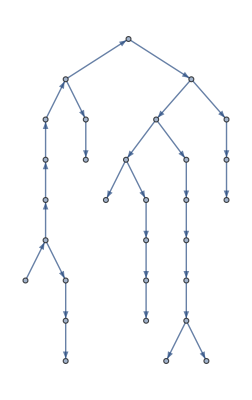

```mathematica
FindSpanningTree[g]
```

```mathematica
FindSpanningTree[g];
HighlightGraph[g,%,GraphHighlightStyle->"Thick"]
```

-Graphics-